```mathematica
■^□
```

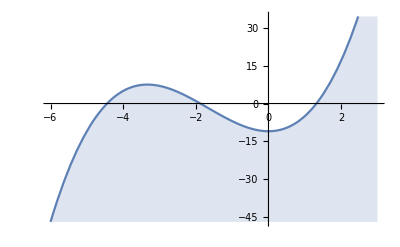

```mathematica
(* 01 *)
Plot[x^3+5 x^2-11,{x,-6,3},Filling->Bottom]
```

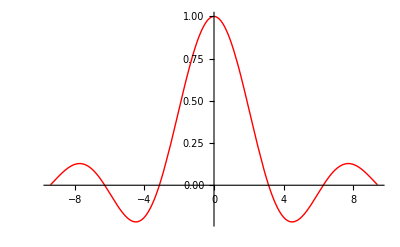

```mathematica
(* 02 *)
```

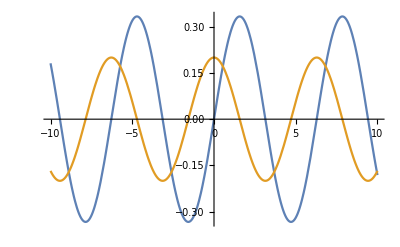

```mathematica
(* 03 *)
Plot[{1/3 Sin[x],1/5 Cos[x]},{x,-10,10}]
```

```mathematica
Show[%60,Axes->False]
```

Show::gtype: Out 不是一个图形类别.

Show[%60,Axes→False]

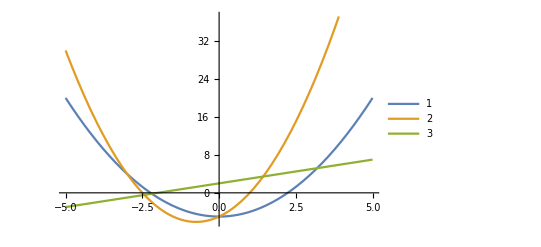

```mathematica
(* 04 *)
Plot[{x^2-5,2 x^2+3x-5,x+2},{x,-5,5},PlotLegends->{"1","2","3"}]
```

```mathematica
(* 05 *)
Plot3D[Sin[x^2-y],{x,-π,π},{y,-π,π}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x^2-y],{x,-π,π},{y,-π,π},PlotPoints->100,MaxRecursion->2]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x^2-y],{x,-π,π},{y,-π,π},Mesh->None,PlotPoints->100,MaxRecursion->2]
```

-Graphics3D-

```mathematica
Show[%8,Axes->False]
```

-Graphics3D-

```mathematica
Show[%9,Boxed->False]
```

-Graphics3D-

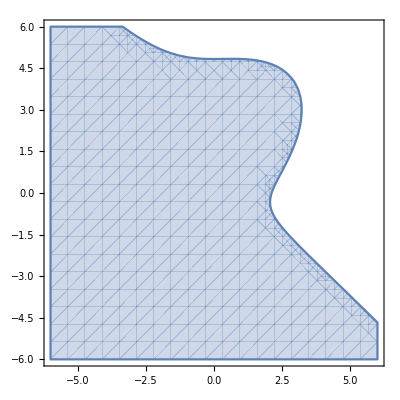

```mathematica
(* 06 *)
```

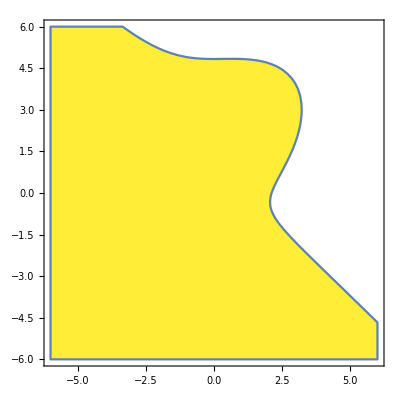

```mathematica
RegionPlot[x x x-x x+y y y-4 y y-3 y<5,{x,-6.,6.},{y,-6.,6.},PlotStyle->RGBColor[1.,0.93,0.22]]
```

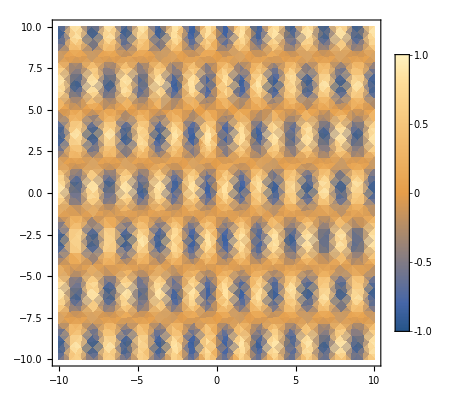

```mathematica
(* 07 *)
DensityPlot[Sin[3x] Sin[y-5],{x,-10,10},{y,-10,10},PlotLegends->Automatic]
```

```mathematica
(* 08 *)
Graph[{a->b,a->c,b->a,b->3,c->d,c->e,d->e,e->a,e->d,e->e}]
```

-Graphics-

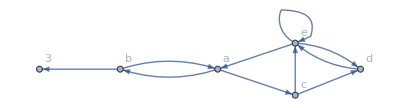

```mathematica
Graph[
{a->b,a->c,b->a,b->3,c->d,c->e,d->e,e->a,e->d,e->e},
DirectedEdges->True,
VertexLabels->Automatic
]
```

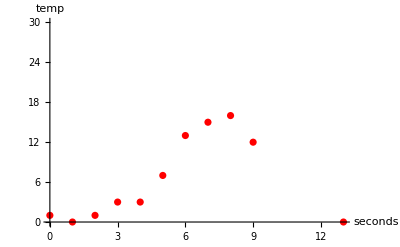

```mathematica
(* 09 *)
ListPlot[
{{0,1},{1,0},{2,1},{3,3},{4,3},{5,7},{6,13},{7,15},{8,16},{9,12},{13,0}},
AxesLabel->{"seconds","temp"},
PlotRange->{0,30},
PlotStyle->Red
]
```

```mathematica
(* 10 *)
BarChart3D[RandomReal[{0,5},{10,5}],ChartLayout->"Stacked"]
```

-Graphics3D-